[ =============================================================================================== ] 
 [ Author: Márton Petö                                                                             ] 
 [ Date: 05.07.2023                                                                                ] 
 [ Affiliation: Otto von Guericke University Magdeburg, Germany                                    ] 
 [ ----------------------------------------------------------------------------------------------- ] 
 [ This Mathematica notebook is a supplementary file for the examples provided in the article      ] 
 [                                                                                                 ] 
 [ CODE VERIFICATION OF IMMERSED BOUNDARY TECHNIQUES USING THE METHOD OF MANUFACTURED SOLUTIONS    ] 
 [ Authors: M. Petö, M. Gorji, F. Duvigneau, A. Düster, D. Juhre, S. Eisenträger                   ] 
 [ Journal: Computational Mechanics                                                                ] 
 [                                                                                                 ] 
 [ ----------------------------------------------------------------------------------------------- ] 
 [ Note 1: The When using the methods or results provided in the paper and supplementary material, ] 
 [ please cite our work accordingly.                                                               ] 
 [ ----------------------------------------------------------------------------------------------- ] 
 [ Note 2: The correct evaluation of this script requires the loading of the functions stored in   ] 
 [ the Mathematica notebook “Utility_functions.nb”.                                                ] 
 [ =============================================================================================== ]

```mathematica
(* DEFINE GEOMETRY *) 
L= 4; xC = {0,0,0}; R = 2;
OmegaCube = ImplicitRegion[x≥0&&x≤L&&y≥0&&y≤L&&z≥0&&z≤L,{x,y,z}];
OmegaInc= ImplicitRegion[(x-xC[[1]])^2+(y-xC[[2]])^2+(z-xC[[3]])^2≤R^2 &&x≥0&& x≤L&&y≥0 && y≤L&&z≥0 && z≤L,{x,y,z}];
OmegaMat =RegionDifference[OmegaCube,OmegaInc]; 
RegionPlot3D[{OmegaInc,OmegaMat}]
```

-Graphics3D-

```mathematica
(* DEFINE DISPLACEMENT FIELD IN SPHERICAL COORDINATES *)
(* Polynomial function of the radius r, whose value is zero at r=R. This is used for the definition of uMat in Eq. (60) *)
poly=s*(r^5-4r^3);
(* Define u, such that the polynomial function for all r<R (=uInc) is scaled by the constant term c efined -> Eq. (61) *)
u = {poly,0,0}*Piecewise[{{c,r≤R}},1];
```

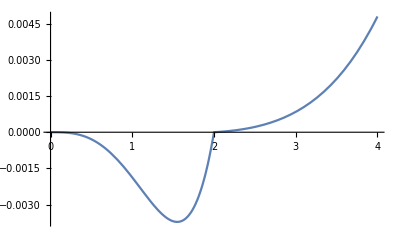

```mathematica
(* PLOT DISPLACEMENT FIELD ALONG CUT LINE. *)
(* Note that for plotting the displacement field, the c-parameter must be defined. Here, c = 100 is *)
(* used and the created plot corresponds to Fig. 10b in the paper. *)
Plot[u[[1]]/.{r->rr,c->100,s->(1/1.6*10^-5)},{r,0,4}]
```

```mathematica
(* MATERIAL PROPERTIES *)
(* Here, the material properties are defined as piece-wise functions, such that for all points with *)
(* r>R, i.e., for the points in the matrix material, lambdaMat and muMat apply, while for all other *)
(* points (i.e. in the inclusion) lambdaInc and muInc. *)
lambda=Piecewise[{{lambdaMat,r≥R}},lambdaInc]
mu=Piecewise[{{muMat,r≥R}},muInc]
```

Piecewise[{{lambdaMat, r≥2}, {lambdaInc, True}}]

Piecewise[{{muMat, r≥2}, {muInc, True}}]

```mathematica
(* COMPUTE STRAIN TENSOR; STRESS TENSOR AND THE RADIAL BODY LOAD *)
(* Compute strain and stress tensors in spherical coordinates, as well as the radial component of the body load *)
epsilon = StrainTensorRadialDispField3D[u]//FullSimplify;
sigma = StressTensorRadialDispField3D[epsilon,lambda,mu]//FullSimplify;
br = -StressDivRadialDispField3D[sigma]//FullSimplify;
```

```mathematica
(* DISPLAY STRAIN, STRESS AND BODY LOAD FIELD EQUATIONS *)
sigma//MatrixForm
epsilon/MatrixForm
br
(* By replacing the Lame constants by E and nu in the radial body force, we get the Eqs (62) and (63) in the paper *)
br/.{lambdaMat->Enu2lambda[EMat,nuMat],muMat->Enu2mu[EMat,nuMat],lambdaInc->Enu2lambda[EInc,nuInc],muInc->Enu2mu[EInc,nuInc]}//FullSimplify
```

(Piecewise[{{c r^2 (-4 (5 lambdaInc+6 muInc)+(7 lambdaInc+10 muInc) r^2) s, r<2}, {r^2 (-4 (5 lambdaMat+6 muMat)+(7 lambdaMat+10 muMat) r^2) s, r>2}, {Indeterminate, True}}] | 0 | 0
0 | Piecewise[{{c r^2 (2 muInc (-4+r^2)+lambdaInc (-20+7 r^2)) s, r<2}, {r^2 (2 muMat (-4+r^2)+lambdaMat (-20+7 r^2)) s, r>2}, {Indeterminate, True}}] | 0
0 | 0 | Piecewise[{{c r^2 (2 muInc (-4+r^2)+lambdaInc (-20+7 r^2)) s, r<2}, {r^2 (2 muMat (-4+r^2)+lambdaMat (-20+7 r^2)) s, r>2}, {Indeterminate, True}}])

{{(r^2 s (r (-4+r^2) (Piecewise[{{0, r≠2}, {Indeterminate, True}}])+(-12+5 r^2) (Piecewise[{{c, r≤2}, {1, True}}])))/MatrixForm,0,0},{0,(r^2 (-4+r^2) s (Piecewise[{{c, r≤2}, {1, True}}]))/MatrixForm,0},{0,0,(r^2 (-4+r^2) s (Piecewise[{{c, r≤2}, {1, True}}]))/MatrixForm}}

Piecewise[{{-4 c (lambdaInc+2 muInc) r (-10+7 r^2) s, r<2}, {-4 (lambdaMat+2 muMat) r (-10+7 r^2) s, r>2}, {Indeterminate, True}}]

Piecewise[{{-(4 c EInc (-1+nuInc) r (-10+7 r^2) s)/(-1+nuInc+2 nuInc^2), r<2}, {-(4 EMat (-1+nuMat) r (-10+7 r^2) s)/(-1+nuMat+2 nuMat^2), r>2}, {Indeterminate, True}}]

```mathematica
(* COMPUTE STRAIN ENERGY *)
(* Note that the evaluation of the current strain energy can take a while... The result corresponds to Eq. (64) *)
SEdens =StrainEnergyDensity[sigma,epsilon]//FullSimplify;
SE=Integrate[SEdens/.{r->Sqrt[x^2+y^2+z^2]},{x,0,L},{y,0,L},{z,0,L}]//FullSimplify
```

SE

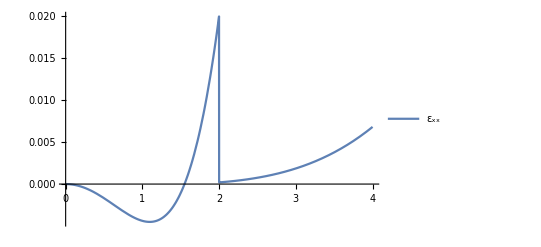

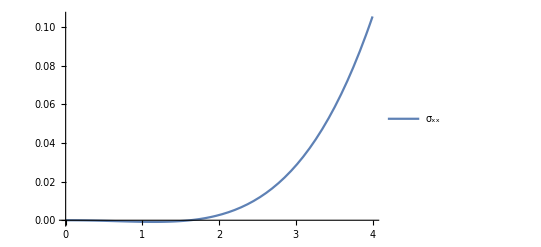

```mathematica
(* NUMERIC VALUE OF THE STRAIN ENERGY *)
(* For a numveric value of the strain energy, the so far symbolic material properties have to be assigned   *)
(* a numeric value. Here, we use the Young's modulus and Possion number to defined the material properties, *)
(* and replace the Lame constants using the functions defined in Utility_functions.nb. The computed strain  *)
(* energy corresponds to value given in Eq. (64). *)
EIncChosen= 1/10;
EMatChosen = 10;
nuIncChosen=3/10;
nuMatChosen=nuIncChosen;
cChosen=100;
sChosen= (1/1.6*10^-5); (* see Eq. (60) *)
lambdaMatChosen=Enu2lambda[EMatChosen,nuMatChosen];
lambdaIncChosen=Enu2lambda[EIncChosen,nuIncChosen];
muMatChosen=Enu2mu[EMatChosen,nuMatChosen];
muIncChosen=Enu2mu[EIncChosen,nuIncChosen];
NumberForm[SE/.{lambdaMat->lambdaMatChosen,lambdaInc->lambdaIncChosen,muMat->muMatChosen,muInc->muIncChosen,s->sChosen,c->cChosen},16]

(* Below, Figs. 10c and 10d are reproduced by chosing the material properties and c-paramter used in the paper. *)
Plot[epsilon[[1,1]]/.{s->sChosen,c->cChosen,r->rr},{rr,0,4},PlotLegends->{"ε_xx"}]
Plot[sigma[[1,1]]/.{lambdaMat->lambdaMatChosen,lambdaInc->lambdaIncChosen,muMat->muMatChosen,muInc->muIncChosen,s->sChosen,c->cChosen,r->rr},{rr,0,4},PlotLegends->{"σ_xx"},PlotRange->Full]
```